# Equazione di Schrödinger

## Alcuni metodi semplici di soluzione:

## Discretizzazione

Appunti Meccanica Quantistica
  G. Paffuti

Il tipo di problema che vogliamo indagare è il problema agli autovalori

H ψ = E ψ ;      H = p^2/(2m) + V[x];

cioè l’equazione di Schrödinger in una dimensione, nel caso di stati legati.

Nella maggior parte dei casi (1) non ha soluzioni analitiche quindi è opportuno avere degli strumenti per ottenere almeno una soluzione approssimata.

Useremo sempre unità naturali,  (in unità naturali ℏ = m = 1), quindi esplicitando le condizioni al bordo (boundary conditions = b.c.)

-1/2 ψ''[x] + V[x] ψ[x] = E ψ[x];                    b.c.:   ψ[xL] = ψ[xR] = 0;

xL, xR sono gli estremi del dominio, in problemi realistici xL = -∞, xR = + ∞.

## Metodo 1 : Discretizzazione

Semplifichiamo drasticamente il problema facendo due approssimazioni

Limitiamoci ad un intervallo finito [xL, xR], xR - xL = L.  Se L è grande rispetto alla zona classicamente permessa ci si aspetta che l’errore sia esponenzialmente piccolo. Ovviamente occorrerà verificare la stabilità al crescere di L.

Discretizziamo lo spazio, scriviamo cioè le derivate come differenze finite e riscriviamo il problema (2) come un problema con un numero finito di incognite, il valore di ψ sui punti della griglia.

### Procedura di discretizzazione

Discretizziamo l' intervallo in punti di distanti h fra loro (h è detto anche passo della griglia)

x[j] = xL + j*h;  j = 1,2,... ,nP;    Punti interni in [xL,xR].

Le incognite del problema diventano i valori di ψ sui punti interni della griglia, i valori al bordo sono invece fissati. 
Sia nP il numero di punti interni, ci saranno nP+1 intervalli di ampiezza h che coprono il segmento di partenza.
Sulla griglia in questione possiamo approssimare le derivate seconde in termini di differenze finite:

Posto:     F[x[j]] ≡ f[j],    F''[x[j]] ≃ ( f[j+1] - 2 f[j] + f[j-1])/h^2;

L'equazione di Schrödinger diventa quindi un sistema lineare omogeneo:

-1/(2 h^2)(ψ[j+1]-2ψ[j] + ψ[j-1]) + V[j] ψ[j] = E ψ[j]

Ci sono nP incognite. I punti estremi hanno valore noto: ψ[0]=ψ[nP+1] = 0. Esplicitamente

-1/(2 h^2)(ψ[2] - 2 ψ[1]               ) + V[1]ψ[1] = E ψ[1];                                                   Eq. 1;
-1/(2 h^2)(ψ[3] - 2 ψ[2] + ψ[1]) + V[2]ψ[2] = E ψ[2];                                                    Eq. 2;
...  ...   ...   ... ;
-1/(2 h^2)(ψ[nP] - 2 ψ[nP-1] + ψ[nP-2]) + V[nP-1]ψ[nP-1] = E ψ[nP-1];      Eq. nP-1;-1/(2 h^2)(             - 2 ψ[nP]       + ψ[nP-1]) + V[nP]ψ[nP] = E ψ[nP];                            Eq.  nP;

Possiamo scrivere in forma compatta l’intero sistema usando delle matrici. Definiamo una matrice D2 che rappresenta la derivata seconda ed un amatrice diagonale che rappresenta i valori del potenziale sulla griglia. La matrice D2 ha una forma tridiagonale, connettendo la diagonale principale solo con le diagonali immediatamente superiore ed inferiore. Si ridurrà il problema alla forma

-1/(2 h^2) D2.ψ + V.ψ = E ψ;               D2 = (-2 | 1 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0
0 | 1 | -2 | 1 | 0
0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 1 | -2);  (nP = 5);

#### Caratteristiche

Vantaggi:   È un metodo molto semplice e flessibile. Le matrici richieste sono sparse, quindi è abbastanza agevole trattare matrici piuttosto grandi.

Svantaggi: Per gli stati eccitati, tipicamente più estesi,  il valore di L  richiesto può essere piuttosto grande.D’altronde è necessario tenere il parametro di discretizzazione h abbastanza piccolo per ridurre gli errori numerici h = L/(nP+1) . Questo comporta la necessità di molti punti e quindi matrici grandi.

## Esempio e caso generale

### Esempio 1: Oscillatore armonico

Si tratta di una particella in un potenziale V[x] = x^2/2. Abbiamo posto ω = 1.

È uno dei pochi casi esattamente risolubili. Lo spettro e le autofunzioni sono dati da  (in queste unità)

E_n = (n+1/2);   ψ_n[x]= 1/π^(1/4)1/(√(2^n n!))H_n[x] Exp[-x^2/2];  n = 0,1 ,2

Questo risultato sarà dimostrato nelle lezioni sull’oscillatore armonico. Hn sono i polinomi di Hermite, in Mathematica sono dati da HermiteH[n,x]. n pari e dispari corrisponde a soluzioni pari e dispari rispettivamente.

```mathematica
V[x_]:= x^2/2;
```

```mathematica
psiHarmonic[n_,x_]:= 1/π^(1/4)1./(√(2^n(n)!))HermiteH[n,x]Exp[-x^2/2];
```

#### Procedura

Definiamo la griglia considerando un intervallo con L = 10;

```mathematica
L = 10; xL = -L/2; xR = L/2;
nP =105;
h = N[(xR - xL)/(nP+1)]; 
xP= xL + h* Range[nP];
```

N.B.:  nP punti interni significa nP+1 intervalli. Se nP è dispari il punto x = 0 appartiene alla griglia.

Definiamo le matrici D2 e V

```mathematica
D2=SparseArray[{Band[{1,1}]-> -2,Band[{2,1}]-> 1,Band[{1,2}]-> 1},{nP,nP}];
matV = SparseArray[Band[{1,1}]-> V[xP],{nP,nP}];
```

La forma discretizzata dell'Hamiltoniana è

```mathematica
Ham = - 1/(2 h^2) D2 + matV;
```

Autovalori ed autovettori possono essere calcolati separatamente o assieme in  Mathematica con le funzioni Eigenvalues and Eigensystem.
Cominceremo dal primo caso, per illustrare come scegliere gli autovalori a cui siamo interessati.

Calcolo di tutti gli autovalori

Il modo più semplice di operare è calcolarsi tutti gli autovalori e succesivamente eseguire il loro ordinamento, con la funzione Sort.

```mathematica
eigAll = Sort[Eigenvalues[Ham]];
eigAll[[Range[1,5]]]
```

Eigenvalues::arh: Because finding 105 out of the 105 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

{0.499722,1.49861,2.49638,3.49303,4.48858}

Come si vede Mathematica ha dato un messaggio di warning: l’uso di matrici sparse è conveniente, nel calcolo degli autovalori, solo se si decide di calcolare una frazione degli autovalori stessi. Se si vogliono tutti conviene usare le matrici in forma normale, che si ottiene con la funzione Normal.

Il lettore interessato alla sintassi di alcuni dei comandi utilizzati consulti la sezione (chiusa) seguente. Per visualizzarla si attivi il triangolo a sinistra del titolo.

Il risultato ottenuto è una ragionevole approssimazione degli autovalori esatti: (0.5, 1.5, 2.5, 3.5, 4.5 ... )

```mathematica
errorePercentuale= (eigAll[[Range[1,5]]]-(0.5+Range[0,4]))/(0.5+Range[0,4])*100
```

{-0.0556558,-0.0928008,-0.144838,-0.199028,-0.253774}

##### Mathematica: note

Funzione SparseArray

Quando si hanno molti elementi di matrice uguale a 0, SparseArray dà un modo efficiente di memorizzare gli elementi non nulli. Si consulti  Mathematica Help per informazioni dettagliate sull’argomento.

Abbiamo usato la funzione Band[{i, j}] per riempire la matrice, questa funzione è presente dalla versione 6 di Mathematica .
Band[{i, j}] riempie la diagonale a partire dall’elemento (i , j) della matrice.

Il modo standard per l’assegnazione dei valori è attraverso l’assegnazione di pattern, ad esempio {i_ , i_ } -> -2 significa che tutti gli elementi diagonali sono posti uguale a -2.

Il pattern

{i_,j_}/;j-i == 1 ....

significa: per ogni i e j se è verificata la condizione j-i = 1 l’elemento è ....

Per la matrice diagonale  matV avremmo anche potuto usare l’indirizzamento diretto, esplicitando gli indirizzi con il vettore indDiag definito sotto. Quindi ad esempio avremmo potuto scrivere:

D2 = SparseArray[{{i_, i_} -> -2, {i_, j_} /; j - i == 1 -> 1,{i_, j_} /; i - j == 1 ->  1}, {nP, nP}];
indDiag = Table[{i, i}, {i, 1, nP}];
matV = SparseArray[indDiag → V[xP]];

La funzione SparseArray è disponibile solo dalla versione 5 di Mathematica , per versioni precedenti si possono usare funzioni come Table per scrivere gli elementi di matrice. Un sempio è il seguente frammento di codice

<< LinearAlgebra`MatrixManipulation`;
D2 = ZeroMatrix[nP];
Table[D2[[i, i]] = -2, {i, 1, nP}];
Table[D2[[i, i + 1]] = 1, {i, 1, nP - 1}];
Table[D2[[i + 1, i]] = 1, {i, 1, nP - 1}];

Funzione Normal

Trasforma una matrice sparsa in una matrice normale (piena).

Funzione Eigenvalues

Il comando  Eigenvalues[M] calcola gli autovalori della matrice M. Il comando ha diverse opzioni, si consulti l’Help di Mathematica .

Se la matrice è sparsa Mathematica usa per il calcolo un algoritmo ricorsivo molto efficiente, che tipicamente è conveniente per ottenere una percentuale (circa il 20%) degli autovalori. Per matrici piene, o per avere tutti gli autovalori, conviene usare come input matrici in forma normale, a cui Mathematica applica una algoritmo standard mutuato dal pacchetto numerico LAPACK. Come è chiearo dal messaggio di warning visto sopra Mathematica passa in modo automatico a questo algoritmo quando è necessario.

Per calcolare solo k degli autovalori l’istruzione è

Eigenvalues[M,k]

In Mathematica gli autovalori sono ordinati in modo decrescente, rispetto al loro modulo. Se vogliamo i k autovalori più piccoli dobbiamo introdurre un numero negativo (cioè si conta dal basso, dalla fine della lista di autovalori). Ad esempio

Eigenvalues[M,-5]

fornisce i primi 5 autovalori, quelli con modulo più piccolo.

I tempi di esecuzione dei comandi precedenti dipendono molto dal processore e dalla versione di Mathematica , non è detto nemmeno che la versione più recente alla prima release sia più veloce: queste routines sono ottimizzate ad un livello abbastanza di base in Mathematica .

Function Eigenvalues 
Eigenvalues[M] compute the eigenvalues of M, it has several extensions to be used in other notebooks and the reader is referred to Mathematica Help for more details.
If M is a sparse matrix Eigenvalues use a recursive and efficient method to find some of the eigenvalues, if the matrix is full or more than 20% of the eigenvalues are requested it is more efficient to switch to a general method, capable of dealing also with arbitrary precision numbers, based on LAPACK routines. In the last instruction we call the function with a sparse matrix and request all the eigenvalues, then automatically Mathematica switched on the full-matrix method and gives us a warning.
To avoid the warning we can either transform our matrix to a Normal form, i.e. non sparse, or request only a few eigenvalues, the last method is usually vastly more efficient. If a number k of eigenvalues is requested the syntax is 
Eigenvalues[M, k]
The eigenvalues are  given in  decreasing absolute value. and k is the k-th eigenvalue. If we want the first k smallest eigenvalues we write a negative entry, i.e.
Eigenvalues[M, -5]
compute the lowest 5 eigenvalues. Below we compare the two methods. The times can change significantly depending on the computer you use, the processor etc. as usually linear algebra routines are optimized at a very low level.

Esempio 1

Matrice piena: usiamo la matrice calcolata sopra e calcoliamo i primi 5 autovalori

```mathematica
eig5 =Sort[ Eigenvalues[Normal[Ham],-5]]//Timing
```

{0.003147,{0.499722,1.49861,2.49638,3.49303,4.48858}}

Con l’algoritmo pe rmatrici sparse:

```mathematica
eig5 =Sort[ Eigenvalues[Ham,-5]]//Timing
```

{0.001499,{0.499722,1.49861,2.49638,3.49303,4.48858}}

Metodo usato da Mathematica

Per il calcolo degli autovalori di una matrice sparsa Mathematica usa un metodo iterativo chiamato Arnoldi, usualmente il metodo è veloce e converge rapidamente al risultato. In caso di problemi è possibile usare un paio di opzioni che facilitano la ricerca degli autovalori: BasisSize e Shift sono due esempi.

BasisSize:  Definisce la dimensione della base di vettori usata per implementare la procedura iterativa

Shift: assegna un valore approssimato ad uno degli autovalori, aiuta in questo modo l’innesco del metodo iterativo.

Diamo un paio di esempi

```mathematica
eig50 =Sort[ Eigenvalues[Ham,-50,Method-> {"Arnoldi","Shift"-> 0}]];//Timing
```

{0.056264,Null}

```mathematica
eig50 =Sort[ Eigenvalues[Ham,-50,Method-> {"Arnoldi","Shift"-> 0,"BasisSize"-> 70}]];//Timing
```

{0.034836,Null}

#### Autofunzioni

Si può usare la funzione Eigenvectors, che fornisce gli autovettori, ma conviene usare Eigensystem che calcola in contemporanea autovalori ed autofunzioni. La sintassi è:

{eigs, eigV} = Eigensystem[matrix]

eigs ed eigV indicano rispettivamente le liste di autovalori ed autofunzioni (vettori sulla griglia di base).
L’autovettore k-esimo è  eigV[[k]].  In pratica eigV è una matrice in cui ogni riga è un autovettore.

Nel seguito diamo un esempio per illustrare anche un possibile metodo di ordinamento degli autovettori ed autovalori prodotti.

Per essere più realistici del caso precedente consideriamo nP = 1000, in questo caso è ovvia l’utilità di usare matrici sparse.

```mathematica
L = 20; xL = -L/2; xR = L/2;
nP =1001;
h = N[(xR - xL)/(nP+1)]; 
xP= xL + h* Range[nP];
```

```mathematica
D2=SparseArray[{Band[{1,1}]-> -2,Band[{2,1}]-> 1,Band[{1,2}]-> 1},{nP,nP}];
matV = SparseArray[Band[{1,1}]-> V[xP],{nP,nP}];
```

```mathematica
Ham = - 1/(2 h^2) D2 + matV;
```

Calcolo degli autovalori ed autovettori :

```mathematica
{ene,vecPsi} = Eigensystem[Ham,-50];
```

La funzione Ordering fornisce l’ordine canonico (dal più piccolo al più grande, per ordinamenti diversi consultare l’Help). L’uscita è l’elenco degli indici ordinati.

```mathematica
order = Ordering[ene];
{ene, vecPsi} = {ene[[order]],vecPsi[[order]]};
```

Un controllo : vecPsi[[[k]] è il k-esimo autovettore:

```mathematica
Max[Table[Norm[ Ham.vecPsi[[k]]-ene[[k]]vecPsi[[k]]],{k,1,Length[ene]}]]
```

2.69639×10^-12

#### Normalizzazione delle autofunzioni

Gli autovettori forniti da Eigensystem sono normalizzati a 1. Indichiamo con c_kil valore sul k-esimo punto della griglia. La norma della funzione, calcolata con la regola del trapezio è (approssimativamente) h-volte la somma dei quadrati della funzione ψ, essendo h l’ampiezza dell’intervallo elementare:

∑ dx ψ[x_k]^2= ∑ h c_k^2 = h

quindi per normalizzare la funzione basta dividere per √h .

Per essere corretti la formula del trapezio, per l’integrale di una funzione f nell’intervallo considerato, sarebbe

∫_x_0^x_m f[x]𝕕x = h[f_0/2+ f_1+f_2+ . . . f_(m-1)+ f_m/2] + 𝒪(h^3)

Siccome la nostra funzione si annulla agli estremi la (3) calcola all’ordine richiesto l’integrale.

Possiamo confrontare le funzioni con il loro valore analitico

```mathematica
puntiGrafico = Transpose[{xP,Sign[vecPsi[[1,100]]] 1/(√h)vecPsi[[1]]}];
```

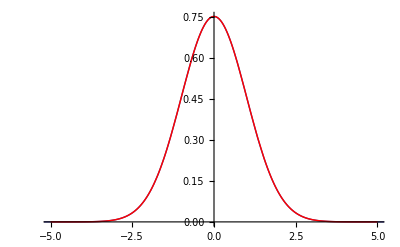

```mathematica
Show[ListPlot[puntiGrafico,Joined-> True,PlotRange-> {{-5,5},All}],
Plot[psiHarmonic[0,x],{x,-5,5},PlotStyle-> Red]]
```

I due grafici sono indistinguibili.

#### Calcolo di elementi di matrice

NOTA: Per il calcolo degli elementi di matrice NON c’è bisogno di introdurre la normalizzazione h: il fattore 1/h dovuto alle due funzioni d’onda si cancella con quello corrispondente in dx (integrale).

Gli indici dei vettori partono da 1, mentre la numerazione degli stati dell’oscillatore parte da 0

Scriviamo gli operatori q, e q^2 sulla griglia

```mathematica
matX = SparseArray[Band[{1,1}]-> xP];
matX2 = SparseArray[Band[{1,1}]-> xP^2];
```

e calcoliamo due elementi di matrice

```mathematica
{vecPsi[[4]].matX.vecPsi[[3]],vecPsi[[4]].matX2.vecPsi[[4]]}
```

{1.22465,3.49938}

L' analogo calcolo sulla base esatta può essere fatto analiticamente ma per chiarezza riportiamo qui il calcolo numerico:

```mathematica
{NIntegrate[ psiHarmonic[3,x]x psiHarmonic[2,x],{x,-∞,∞}],
NIntegrate[ psiHarmonic[3,x] x^2 psiHarmonic[3,x],{x,-∞,∞}]}
```

{1.22474,3.5}

Volendo possiamo scegliere il segno (arbitrario) del vettore numerico in modo da accordarsi con la funzione teorica

```mathematica
ptcheck = Floor[nP/2]+10;
sign= Table[Sign[psiHarmonic[k-1,xP[[ptcheck]]]/vecPsi[[k]][[ptcheck]]],{k,1,Length[vecPsi]}];
Table[vecPsi[[k]] = sign[[k]]*vecPsi[[k]],{k,1,Length[vecPsi]}];
```

#### Funzione interpolante

Mathematica fornisce un modo semplice per costruire una funzione interpolante a partire da coppie ordinate (x,y).

Nel caso in esame conviene aggiungere i punti estremi dell’intervallo, sia per i valori x che per i valori della funzione, che ha valore 0 in entrambe le estremità. Si può fare l’estensione usando Join, che unisce stringhe, o PadRight che ha come sintassi

PadRight[vec,newdim,pad,left]

dove newdim è la nuova lunghezza desiderata, pad l’elemento da inserire e left eventuali elementi da mettere a sinistra. Mostriamo un esempio sul primo vettore, usando entrambe le possibilità:

```mathematica
xExtended = Join[{xP[[1]]-h},xP,{xP[[nP]]+h}];
vecesteso = PadRight[vecPsi[[1]]/Sqrt[h],nP+2,0,1];
```

Interpolation effettua l’interpolazione. Notare l’inclusione del fattore di normalizzazione 1/√h .

```mathematica
fprova = Interpolation[Transpose[{xExtended,vecesteso}]]
```

InterpolatingFunction[{{-10.,10.}},<>]

A questo punto fprova si comporta come una qualunque funzione, ad esempio si può fare un grafico, fare la derivata o l’integrale.
Vediamo ad esempio che il grafico è indistinguibile dalla soluzione esatta:

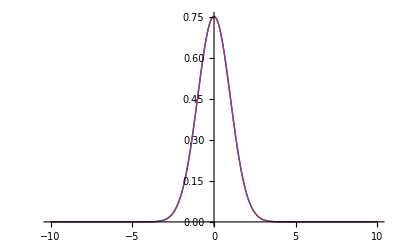

```mathematica
Plot[{fprova[x],psiHarmonic[0,x]},{x,-L/2,L/2},PlotRange-> All]
```

Con la funzione interpolante è banale calcolare ad esempio le derivate e i corrispondenti elementi di matrice di p.

### Caso generale

Come si evince da quanto scritto sopra l’unica cosa che cambia da un potenziale all’altro è la definizione di V[x].

Conviene a questo punto scrivere una funzione che accetti come input una funzione di x come potenziale e, fissati il numero di autovalori richiesti, restituiscala soluzione. Un esempio è la funzione seguente. Ha come input:

Il nome della funzione potenziale

Il numero di autovalori richiesti

un vettore a 2 componenti {nP, L} che dice quanti punti interni prendere e quale valore di L scegliere per la scatola

Ha come output una stringa di tre elementi che sono rispettivamente

Le coordinate della griglia di punti

Un vettore contenente gli autovalori

Un vettore (matrice) per gli autovettori.

Nota : si usa l’opzione Shift in Eigensystem

```mathematica
solveSch[V_,numEig_,{nP_,L_}]:=
Module[{xL,xR,h,indDiag,D2,Ham,matV,ene,ψ,norm,xP,minV},
xL = -L/2; xR = L/2;
h = N[(xR - xL)/(nP+1)]; 
xP= xL + h* Range[nP];
D2 = SparseArray[{{i_,i_} ->  -2,{i_,j_}/;j-i==1-> 1,
{i_,j_}/; i-j== 1->  1},{nP,nP}];
indDiag = Table[{i,i},{i,1,nP}];
     matV = SparseArray[indDiag-> V[xP]];
minV = Min[V[xP]];
Ham =- 1/(2 h^2) D2 + matV;
{ene,ψ}=Eigensystem[Ham,numEig, Method-> {"Arnoldi","Shift"->( minV-0.01)}];
order = Ordering[ene];
ene = ene[[order]];
ψ = ψ[[order]]/Sqrt[h];
{xP,ene,ψ}]
```

Ad esempio per un oscillatore anarmonico

```mathematica
g=1;
V[x_]:= 1/2 x^2 + 1/2 g x^4;
```

```mathematica
{numEig,nP,L} = {5,1001,20};
```

```mathematica
{xP,ene,psi}= solveSch[V,numEig,{nP,L}];
```

```mathematica
ene
```

{0.696144,2.32419,4.32684,6.57684,9.02585}